# Kerr Effect

## Loading Stuffs I might need

```mathematica
ClearSystemCache[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ClearAll[ErrorForm]
ErrorForm[{x_?NumberQ,Δx_?NumberQ},dgts_:2]:=ToString[PaddedForm[N[Round[x,10^(-dgts)]],{dgts+2,dgts}]]<>" ±"<>ToString[PaddedForm[N[Ceiling[Abs[Δx],10^(-dgts)]],{dgts+1,dgts}]]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed]
};
```

```mathematica
niceStyle2={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Dashed]
};
```

## Loading Data

the following expression imports the whole ods with the kerr data

```mathematica
data=Import["kerr_data.ods"];
```

### this takes the first two sheets for the calibration task

```mathematica
calib1 =Drop[data⟦1⟧ᵀ⟦{1,2}⟧ᵀ,1];
```

```mathematica
calib2 =Drop[data⟦2⟧ᵀ⟦{1,2}⟧ᵀ,1];
```

### this takes sheets 3 to 6 for the easy axis in the first task and replaces the current by the magnetic fields for task 1

```mathematica
easyaxis1=Replace[Drop[data⟦3⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
easyaxis2=Replace[Drop[data⟦4⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
easyaxis3=Replace[Drop[data⟦5⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
easyaxis4=Replace[Drop[data⟦6⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

### this takes sheets 7 to 10 for the hard axis in the first task and replaces the current by the magnetic fields for task 1

```mathematica
hardaxis1=Replace[Drop[data⟦7⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
hardaxis2=Replace[Drop[data⟦8⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
hardaxis3=Replace[Drop[data⟦9⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
hardaxis4=Replace[Drop[data⟦10⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

### this takes sheets 11 to 25 with the hysteresis curves from task 2

```mathematica
a2angle12450=Replace[Drop[data⟦11⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12500=Replace[Drop[data⟦12⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12550=Replace[Drop[data⟦13⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12600=Replace[Drop[data⟦14⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12650=Replace[Drop[data⟦15⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12625=Replace[Drop[data⟦16⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12700=Replace[Drop[data⟦17⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12750=Replace[Drop[data⟦18⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12800=Replace[Drop[data⟦19⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12850=Replace[Drop[data⟦20⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12900=Replace[Drop[data⟦21⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle12950=Replace[Drop[data⟦22⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle13000=Replace[Drop[data⟦23⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle13050=Replace[Drop[data⟦24⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

```mathematica
a2angle13100=Replace[Drop[data⟦25⟧ᵀ⟦{1,2}⟧ᵀ,1],{amps_,volts_}->{30.14*amps,volts},2];
```

### this is the contrast data for task 2, the important stuff

```mathematica
a2results=Drop[data⟦26⟧ᵀ⟦{1,2,3,4,5,6}⟧ᵀ,1]
```

{{124.5,0.142,0.022,0.003,0.805,0.005025},{125,0.113,0.036,0.003,0.536,0.00368},{125.5,-0.028,-0.064,0.003,0.536,0.00368},{126,-0.018,-0.01,0.003,0.536,0.00368},{126.25,0.472,0.504,0.003,0.133,0.001665},{126.5,0.147,0.197,0.003,0.536,0.00368},{127,0.473,0.565,0.003,0.536,0.00368},{127.5,-0.402,-0.266,0.003,1.92,0.0106},{128,0.252,0.434,0.003,1.92,0.0106},{128.5,-0.446,-0.22,0.003,3.479,0.018395},{129,0.551,0.822,0.003,3.479,0.018395},{129.5,-0.541,-0.224,0.003,5.752,0.02976},{130,-0.693,-0.338,0.003,7.146,0.03673},{130.5,-0.773,-0.368,0.003,8.714,0.04457}}

```mathematica
a2resultsA=Drop[data⟦27⟧ᵀ⟦{1,2,3,4,5,6}⟧ᵀ,1];
```

```mathematica
a2resultsnt=Drop[data⟦26⟧ᵀ⟦{8,9,10,11,12,13}⟧ᵀ,1];
```

```mathematica
a2resultsntA=Drop[data⟦27⟧ᵀ⟦{8,9,10,11,12,13}⟧ᵀ,1];
```

### this takes sheets 39 and 48 for task 3 in s-polarization and p-polarization

```mathematica
a3resultsS=Drop[data⟦39⟧ᵀ⟦{1,2,3,4,5,6}⟧ᵀ,1];
```

```mathematica
a3resultsP=Drop[data⟦48⟧ᵀ⟦{1,2,3,4,5,6}⟧ᵀ,1];
```

## Calibrating the Magnetic Field

### border

Remember, we measured 117.2mT at the border

```mathematica
(a1center=Replace[calib1,{amps_,volts_}->{amps,100*volts},2]);
```

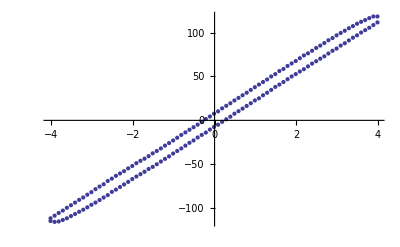

```mathematica
ListPlot[a1center]
```

So, dass sind die linearen Fits für den oberen und unteren Teil der Hysteresekurve (1 und 2)

```mathematica
fita1center1=NonlinearModelFit[
Select[a1center⟦;;Round[Length[a1center]/2]⟧,-2≤#⟦1⟧≤2&],
m x+n,{m,n},x
]
```

FittedModel[7.93717+30.1479 x]

```mathematica
fita1center2=NonlinearModelFit[
Select[a1center⟦Round[Length[a1center]/2];;⟧,-2≤#⟦1⟧≤2&],
m x+n,{m,n},x
]
```

FittedModel[-7.16477+30.1325 x]

Error Form (defined above) takes a list (x,Δx) and puts it in error form with n significant digits (here 3).
BestFitParameters gives the fit parameters, ParameterErrors followed by the appropriate number gives the error of the appropriate fit parameter.
The Error given in the back of the following expression is the error propagation for the arithmetic mean.

```mathematica
ErrorForm[{
Mean[{(m/.fita1center1["BestFitParameters"]),(m/.fita1center2["BestFitParameters"])}],
(√((fita1center1["ParameterErrors"]⟦1⟧)^2+(fita1center2["ParameterErrors"]⟦1⟧)^2))/2
},3]
```

30.140 ± 0.026

```mathematica
ErrorForm[{
Mean[{(n/.fita1center1["BestFitParameters"]),(n/.fita1center2["BestFitParameters"])}],
(√((fita1center1["ParameterErrors"]⟦2⟧)^2+(fita1center2["ParameterErrors"]⟦2⟧)^2))/2
},3]
```

0.386 ± 0.030

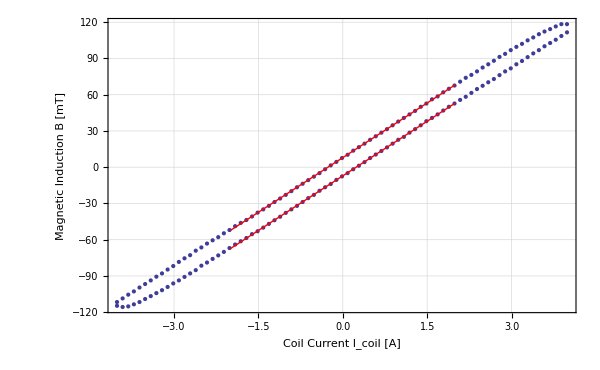

-Graphics-

```mathematica
Show[ListPlot[a1center],Plot[{Normal[fita1center1],Normal[fita1center2]},{x,-2,2},PlotStyle->Directive[Thick,Red]],niceStyle,FrameLabel->{"Coil Current I_coil [A]","Magnetic Induction B [mT]"}]
```

### center

Remember, we measured 123.6mT in the center

```mathematica
(a1border=Replace[calib2,{amps_,volts_}->{amps,100*volts},2]);
```

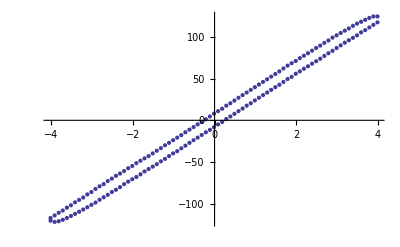

```mathematica
ListPlot[a1border]
```

```mathematica
fita1border1=NonlinearModelFit[
Select[a1border⟦;;Round[Length[a1border]/2]⟧,-2≤#⟦1⟧≤2&],
m x+n,{m,n},x
]
```

FittedModel[8.41365+31.7736 x]

```mathematica
fita1border2=NonlinearModelFit[
Select[a1border⟦Round[Length[a1border]/2];;⟧,-2≤#⟦1⟧≤2&],
m x+n,{m,n},x
]
```

FittedModel[-7.56975+31.7985 x]

```mathematica
ErrorForm[{
Mean[{(m/.fita1border1["BestFitParameters"]),(m/.fita1border2["BestFitParameters"])}],
(√((fita1center1["ParameterErrors"]⟦1⟧)^2+(fita1center2["ParameterErrors"]⟦1⟧)^2))/2
},3]
```

31.786 ± 0.026

```mathematica
ErrorForm[{
Mean[{(n/.fita1border1["BestFitParameters"]),(n/.fita1border2["BestFitParameters"])}],
(√((fita1center1["ParameterErrors"]⟦2⟧)^2+(fita1center2["ParameterErrors"]⟦2⟧)^2))/2
},3]
```

0.422 ± 0.030

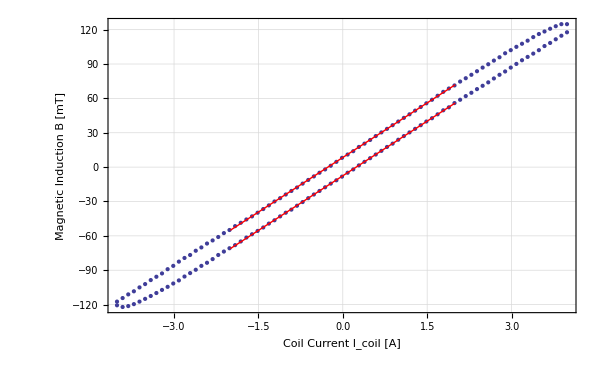

```mathematica
Show[ListPlot[a1border],Plot[{Normal[fita1border1],Normal[fita1border2]},{x,-2,2},PlotStyle->Directive[Thick,Red]],niceStyle,FrameLabel->{"Coil Current I_coil [A]","Magnetic Induction B [mT]"}]
```

## Magnetic Anisotropy

### easy axis (100)

```mathematica
ListLinePlot[easyaxis1];
```

```mathematica
ListLinePlot[easyaxis2];
```

```mathematica
ListLinePlot[easyaxis3];
```

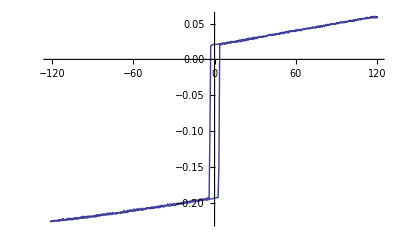

```mathematica
ListLinePlot[easyaxis4]
```

### hard axis (110)

```mathematica
ListLinePlot[hardaxis1];
```

```mathematica
ListLinePlot[hardaxis2];
```

```mathematica
ListLinePlot[hardaxis3];
```

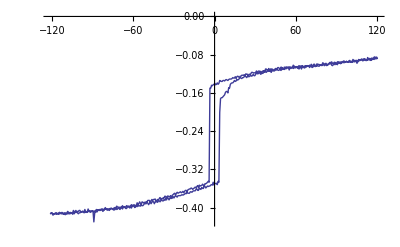

```mathematica
ListLinePlot[hardaxis4]
```

### both together

#### groundwork

```mathematica
easyaxis4C=Replace[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&],{amps_,volts_}->{amps,1/(Max[Drop[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]]-Min[Drop[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])(volts+0.5*(Max[Drop[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]]-Min[Drop[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])-Max[Drop[Select[Select[easyaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])},2];
```

```mathematica
hardaxis4C=Replace[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&],{amps_,volts_}->{amps,1/(Max[Drop[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]]-Min[Drop[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])(volts+0.5*(Max[Drop[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]]-Min[Drop[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])-Max[Drop[Select[Select[hardaxis4,First[#]<65&],First[#]>-65&]ᵀ,1]])},2];
```

```mathematica
fita1e1=NonlinearModelFit[Select[Take[easyaxis4C,Length[easyaxis4C]/2],#⟦2⟧>0.3&],m*x+n,{m,n},x]
```

FittedModel[0.415789+0.00131693 x]

```mathematica
fita1e2=NonlinearModelFit[Select[Take[easyaxis4C,Length[easyaxis4C]/2],#⟦2⟧<-0.3&],m*x+n,{m,n},x]
```

FittedModel[-0.417257+0.00114909 x]

```mathematica
fita1e3=NonlinearModelFit[Select[Drop[easyaxis4C,Length[easyaxis4C]/2],#⟦2⟧<-0.3&],m*x+n,{m,n},x]
```

FittedModel[-0.423176+0.00115065 x]

```mathematica
fita1e4=NonlinearModelFit[Select[Drop[easyaxis4C,Length[easyaxis4C]/2],#⟦2⟧>0.3&],m*x+n,{m,n},x]
```

FittedModel[0.409916+0.00136264 x]

```mathematica
fita1h1=NonlinearModelFit[Select[Select[Take[hardaxis4C,Length[hardaxis4C]/2],#⟦2⟧>0.2&],#⟦1⟧<30&],m*x+n,{m,n},x]
```

FittedModel[0.36764+0.00287468 x]

```mathematica
fita1h2=NonlinearModelFit[Select[Select[Take[hardaxis4C,Length[hardaxis4C]/2],#⟦2⟧<-0.2&],#⟦1⟧>-30&],m*x+n,{m,n},x]
```

FittedModel[-0.306317+0.00322043 x]

```mathematica
fita1h3=NonlinearModelFit[Select[Select[Drop[hardaxis4C,Length[hardaxis4C]/2],#⟦2⟧<-0.2&],#⟦1⟧>-30&],m*x+n,{m,n},x]
```

FittedModel[-0.328586+0.0031659 x]

```mathematica
fita1h4=NonlinearModelFit[Select[Select[Drop[hardaxis4C,Length[hardaxis4C]/2],#⟦2⟧>0.2&],#⟦1⟧<20&],m*x+n,{m,n},x]
```

FittedModel[0.222827+0.0105907 x]

```mathematica
fita1h5=NonlinearModelFit[Select[Select[Select[Drop[hardaxis4C,Length[hardaxis4C]/2],#⟦2⟧>0.2&],#⟦1⟧>20&],#⟦1⟧<30&],m*x+n,{m,n},x]
```

FittedModel[0.373655+0.00192457 x]

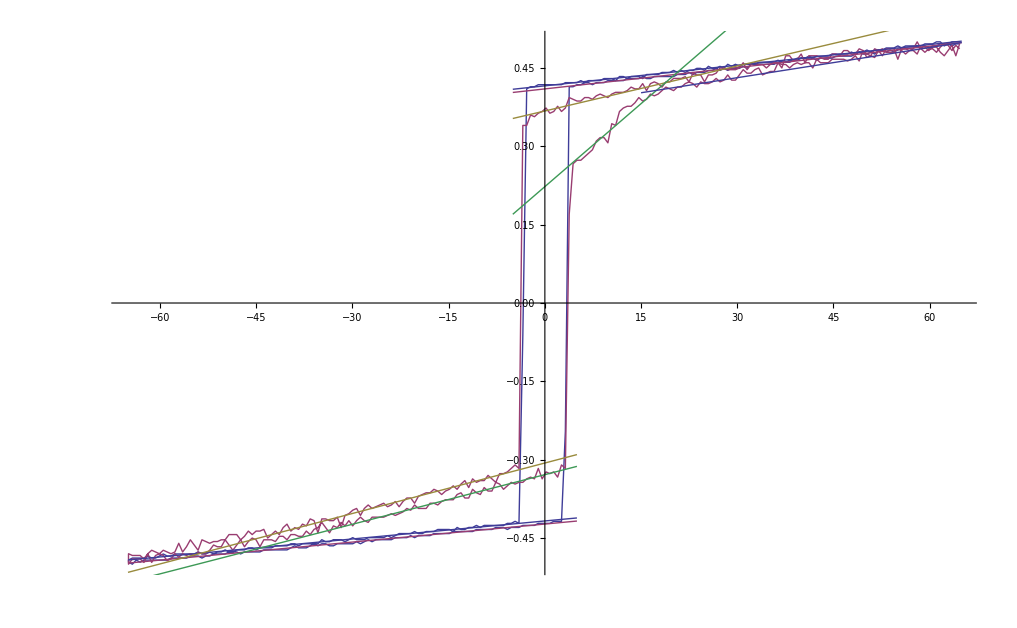

```mathematica
Show[ListLinePlot[{easyaxis4C,hardaxis4C}],Plot[{Normal[fita1e1],Normal[fita1e4],Normal[fita1h1],Normal[fita1h4]},{x,-5,65}],Plot[{Normal[fita1e2],Normal[fita1e3],Normal[fita1h2],Normal[fita1h3]},{x,-65,5}],Plot[Normal[fita1h5],{x,15,65}]]
```

#### final stuff

```mathematica
easyaxis4D=Replace[easyaxis4C,{amps_,volts_}->{amps,(2.1*volts)/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]},2];
```

```mathematica
hardaxis4D=Replace[hardaxis4C,{amps_,volts_}->{amps,(2.1*volts)/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]},2];
```

```mathematica
fita1e1D=NonlinearModelFit[Select[Take[easyaxis4D,Length[easyaxis4D]/2],#⟦2⟧>0.3/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],m*x+n,{m,n},x]
```

FittedModel[2.09624+0.00663941 x]

```mathematica
fita1e2D=NonlinearModelFit[Select[Take[easyaxis4D,Length[easyaxis4D]/2],#⟦2⟧<-0.3/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],m*x+n,{m,n},x]
```

FittedModel[-2.10364+0.00579327 x]

```mathematica
fita1e3D=NonlinearModelFit[Select[Drop[easyaxis4D,Length[easyaxis4D]/2],#⟦2⟧<-0.3/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],m*x+n,{m,n},x]
```

FittedModel[-2.10533+0.00646489 x]

```mathematica
fita1e4D=NonlinearModelFit[Select[Drop[easyaxis4D,Length[easyaxis4D]/2],#⟦2⟧>0.3/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],m*x+n,{m,n},x]
```

FittedModel[2.06663+0.0068699 x]

```mathematica
fita1h1D=NonlinearModelFit[Select[Select[Take[hardaxis4D,Length[hardaxis4D]/2],#⟦2⟧>0.2/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],#⟦1⟧<30&],m*x+n,{m,n},x]
```

FittedModel[1.8535+0.014493 x]

```mathematica
fita1h2D=NonlinearModelFit[Select[Select[Take[hardaxis4D,Length[hardaxis4D]/2],#⟦2⟧<-0.2/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],#⟦1⟧>-30&],m*x+n,{m,n},x]
```

FittedModel[-1.54433+0.0162361 x]

```mathematica
fita1h3D=NonlinearModelFit[Select[Select[Drop[hardaxis4D,Length[hardaxis4D]/2],#⟦2⟧<-0.2/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],#⟦1⟧>-30&],m*x+n,{m,n},x]
```

FittedModel[-1.6566+0.0159612 x]

```mathematica
fita1h4D=NonlinearModelFit[Select[Select[Drop[hardaxis4D,Length[hardaxis4D]/2],#⟦2⟧>0.2/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],#⟦1⟧<20&],m*x+n,{m,n},x]
```

FittedModel[1.03417+0.05957 x]

```mathematica
fita1h5D=NonlinearModelFit[Select[Select[Select[Drop[hardaxis4D,Length[hardaxis4D]/2],#⟦2⟧>0.2/Mean[{Abs[n/.fita1e1["BestFitParameters"]],Abs[n/.fita1e2["BestFitParameters"]],Abs[n/.fita1e3["BestFitParameters"]],Abs[n/.fita1e4["BestFitParameters"]]}]&],#⟦1⟧>20&],#⟦1⟧<30&],m*x+n,{m,n},x]
```

FittedModel[1.88382+0.00970291 x]

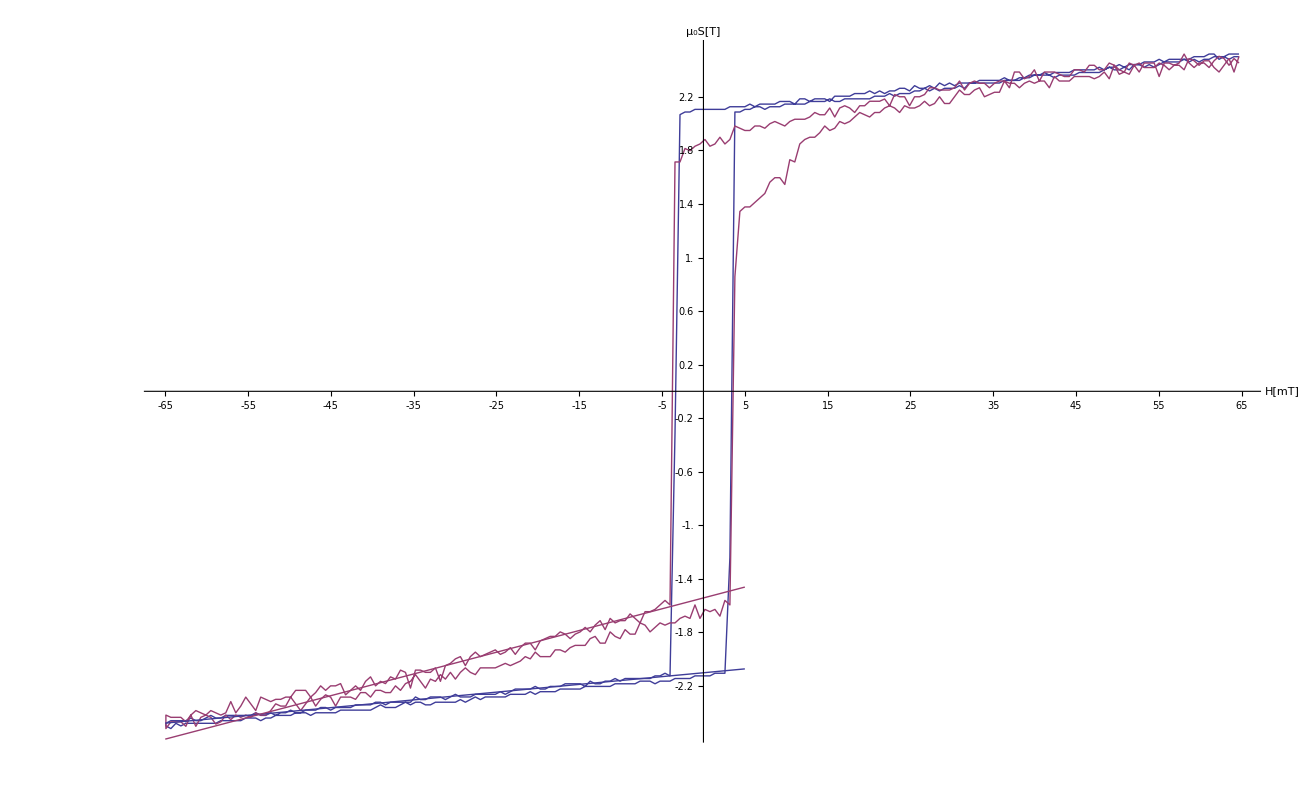

```mathematica
Show[ListLinePlot[{easyaxis4D,hardaxis4D},Ticks->{FindDivisions[{-65,65,5},30],FindDivisions[{-2.2,2.2,0.2},22]},AxesLabel->{"H[mT]","μ_0S[T]"}],Plot[{Normal[fita1e2D],Normal[fita1h2D]},{x,-65,5}]]
```

Das sind die Flaechen zwischen den oberen linearen Fits

```mathematica
aarea=Integrate[Normal[fita1e1D]-Normal[fita1h1D],{x,-3.5,x/.Solve[Normal[fita1e1D]==Normal[fita1h1D],x]⟦1⟧}]
```

4.64916

```mathematica
aerror=aarea*√((0.5/3.5)^2+(√((fita1e1D["ParameterErrors"]⟦2⟧)^2+(fita1h1D["ParameterErrors"]⟦2⟧)^2)/((Mean[{Abs[n/.fita1e1D["BestFitParameters"]],Abs[n/.fita1e2D["BestFitParameters"]],Abs[n/.fita1e3D["BestFitParameters"]],Abs[n/.fita1e4D["BestFitParameters"]]}])-Abs[(n/.fita1h1D["BestFitParameters"])]))^2)
```

0.680795

```mathematica
ErrorForm[{aarea,aerror}]
```

4.65 ± 0.69

```mathematica
barea=Integrate[Normal[fita1e4D],{x,3.5,x/.Solve[Normal[fita1e4D]==Normal[fita1h5D],x]⟦1⟧}]-Integrate[Normal[fita1h4D],{x,3.5,x/.Solve[Normal[fita1h4D]==Normal[fita1h5D],x]⟦1⟧}]-Integrate[Normal[fita1h5D],{x,x/.Solve[Normal[fita1h4D]==Normal[fita1h5D],x]⟦1⟧,x/.Solve[Normal[fita1h5D]==Normal[fita1e4D],x]⟦1⟧}]
```

9.84581

```mathematica
berror=barea*√((0.5/3.5)^2+(√((fita1e4D["ParameterErrors"]⟦2⟧)^2+(fita1h4D["ParameterErrors"]⟦2⟧)^2)/((Mean[{Abs[n/.fita1e1D["BestFitParameters"]],Abs[n/.fita1e2D["BestFitParameters"]],Abs[n/.fita1e3D["BestFitParameters"]],Abs[n/.fita1e4D["BestFitParameters"]]}])-Abs[(n/.fita1h4D["BestFitParameters"])]))^2)
```

1.49225

```mathematica
ErrorForm[{barea,berror}]
```

9.85 ± 1.50

und das die zwischen den unteren beiden

```mathematica
carea=Abs[Integrate[Normal[fita1e2D]-Normal[fita1h2D],{x,x/.Solve[Normal[fita1e2D]==Normal[fita1h2D],x]⟦1⟧,-3.5}]]
```

13.0848

```mathematica
cerror=carea*√((0.5/3.5)^2+(√((fita1e2D["ParameterErrors"]⟦2⟧)^2+(fita1h2D["ParameterErrors"]⟦2⟧)^2)/((Mean[{Abs[n/.fita1e1D["BestFitParameters"]],Abs[n/.fita1e2D["BestFitParameters"]],Abs[n/.fita1e3D["BestFitParameters"]],Abs[n/.fita1e4D["BestFitParameters"]]}])-Abs[(n/.fita1h2D["BestFitParameters"])]))^2)
```

1.88588

```mathematica
ErrorForm[{carea,cerror}]
```

13.08 ± 1.89

```mathematica
darea=Abs[Integrate[Normal[fita1e3D]-Normal[fita1h3D],{x,x/.Solve[Normal[fita1e3D]==Normal[fita1h3D],x]⟦1⟧,3.5}]]
```

12.2308

```mathematica
derror=darea*√((0.5/3.5)^2+(√((fita1e3D["ParameterErrors"]⟦2⟧)^2+(fita1h3D["ParameterErrors"]⟦2⟧)^2)/((Mean[{Abs[n/.fita1e1D["BestFitParameters"]],Abs[n/.fita1e2D["BestFitParameters"]],Abs[n/.fita1e3D["BestFitParameters"]],Abs[n/.fita1e4D["BestFitParameters"]]}])-Abs[(n/.fita1h3D["BestFitParameters"])]))^2)
```

1.79928

```mathematica
ErrorForm[{darea,derror}]
```

12.23 ± 1.80

mittel ueber alle

```mathematica
ErrorForm[{10^-3/(4*Pi*10^-7)*4/1000*Mean[{aarea,barea,carea,darea}],10^-3/(4*Pi*10^-7)*4/1000*1/4 √(aerror^2+berror^2+cerror^2+derror^2)},1]
```

31.7 ± 2.5

mittel ohne erstes

```mathematica
ErrorForm[{10^-3/(4*Pi*10^-7)*4/1000*Mean[{barea,carea,darea}],10^-3/(4*Pi*10^-7)*4/1000*1/4 √(berror^2+cerror^2+derror^2)},1]
```

37.3 ± 2.4

mittel ueber obere

```mathematica
ErrorForm[{10^-3/(4*Pi*10^-7)*4/1000*Mean[{aarea,barea}],10^-3/(4*Pi*10^-7)*4/1000*1/4 √(aerror^2+berror^2)},1]
```

23.1 ± 1.4

mittel ueber untere

```mathematica
ErrorForm[{10^-3/(4*Pi*10^-7)*4/1000*Mean[{carea,darea}],10^-3/(4*Pi*10^-7)*4/1000*1/4 √(cerror^2+derror^2)},1]
```

40.3 ± 2.1

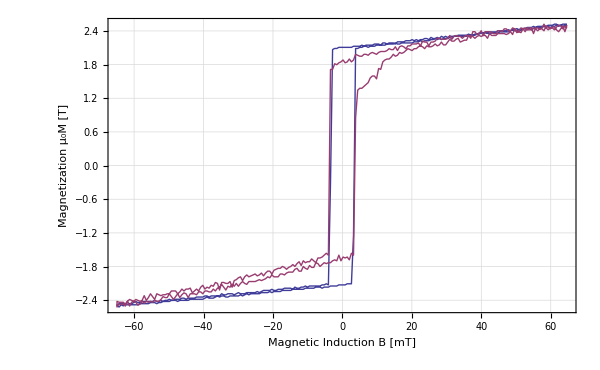

```mathematica
Show[ListLinePlot[{easyaxis4D,hardaxis4D}],niceStyle,FrameLabel->{"Magnetic Induction B [mT]","Magnetization μ_0M [T]"}]
```

```mathematica
.
```

## Kerr Rotation Angle

### plots of the hysteresis curves

```mathematica
ListPlot[a2angle12450];
```

```mathematica
ListPlot[a2angle12500];
```

```mathematica
ListPlot[a2angle12550];
```

```mathematica
ListLinePlot[a2angle12600];
```

```mathematica
ListLinePlot[a2angle12625];
```

```mathematica
ListPlot[a2angle12650];
```

```mathematica
ListPlot[a2angle12700];
```

```mathematica
ListLinePlot[a2angle12750];
```

```mathematica
ListPlot[a2angle12800];
```

```mathematica
ListPlot[a2angle12850];
```

```mathematica
ListPlot[a2angle12900];
```

```mathematica
ListPlot[a2angle12950];
```

```mathematica
ListPlot[a2angle13000];
```

```mathematica
ListPlot[a2angle13050];
```

### fit for kerr angle

#### making the contrast data

```mathematica
(contrast=Replace[a2results,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm;
```

```mathematica
(inversecontrast=Replace[contrast,{angle_,contrastt_,error_}->{angle,1/contrastt,error/contrastt^2},2])//TableForm;
```

```mathematica
(contrastA=Replace[a2resultsA,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm;
```

```mathematica
(inversecontrastA=Replace[contrastA,{angle_,contrastt_,error_}->{angle,1/contrastt,error/contrastt^2},2])//TableForm;
```

```mathematica
(contrastnt=Replace[a2resultsnt,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm;
```

```mathematica
(inversecontrastnt=Replace[contrastnt,{angle_,contrastt_,error_}->{angle,1/contrastt,error/contrastt^2},2])//TableForm;
```

```mathematica
(contrastntA=Replace[a2resultsntA,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm;
```

```mathematica
(inversecontrastntA=Replace[contrastntA,{angle_,contrastt_,error_}->{angle,1/contrastt,error/contrastt^2},2])//TableForm;
```

#### making the fits

```mathematica
fita2invlin=NonlinearModelFit[Drop[Drop[inversecontrastᵀ,-1]ᵀ,8],m*x+n,{m,n},x,
Weights->(Drop[inversecontrast,8]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&)]
```

FittedModel[770.343-6.21136 x]

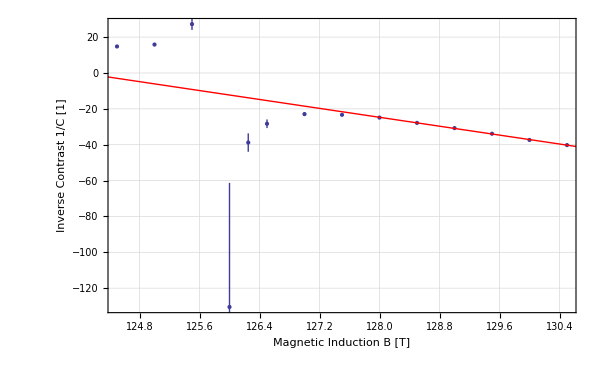

```mathematica
Show[ErrorListPlot[inversecontrast],Plot[Normal[fita2invlin],{x,124,131},PlotStyle->Red],niceStyle,FrameLabel->{"Magnetic Induction B [T]","Inverse Contrast 1/C [1]"}]
```

```mathematica
fita2invall=NonlinearModelFit[Drop[Drop[inversecontrastᵀ,-1]ᵀ,3],a*(x-c)+b/(x-c),{{a,-10},{b,-100},{c,125}},x,
Weights->(Drop[inversecontrast,3]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.99]
```

FittedModel[-16.983/(-125.751+x)-7.79658 (-125.751+x)]

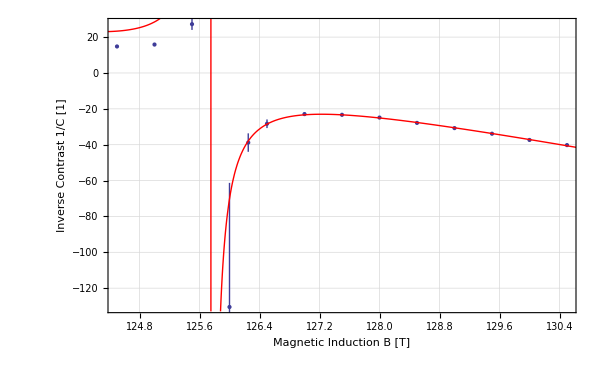

```mathematica
Show[ErrorListPlot[inversecontrast],Plot[Normal[fita2invall],{x,124,131},PlotStyle->Red],niceStyle,FrameLabel->{"Magnetic Induction B [T]","Inverse Contrast 1/C [1]"}]
```

```mathematica
fita2inv=NonlinearModelFit[Drop[Drop[inversecontrastAᵀ,-1]ᵀ,0],a*(x-c)+b/(x-c),{{a,-10},{b,-100},{c,126}},x,
Weights->(Drop[inversecontrastA,0]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.99]
```

FittedModel[-9.22269/(-125.795+x)-8.4384 (-125.795+x)]

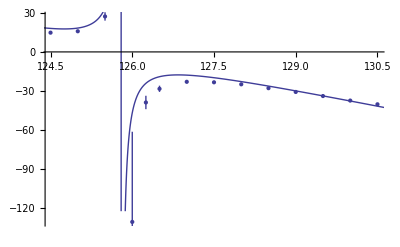

```mathematica
Show[ErrorListPlot[inversecontrast],Plot[Normal[fita2inv],{x,124,131}]]
```

```mathematica
fita2all=NonlinearModelFit[Drop[Drop[contrastᵀ,-1]ᵀ,0],(a*(x-c))/((x-c)^2+b),{a,b,{c,125}},x,
Weights->(Drop[contrast,0]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.99,
MaxIterations->1000000]
```

FittedModel[-(0.118942 (-125.904+x))/(1.50042+(-125.904+x)^2)]

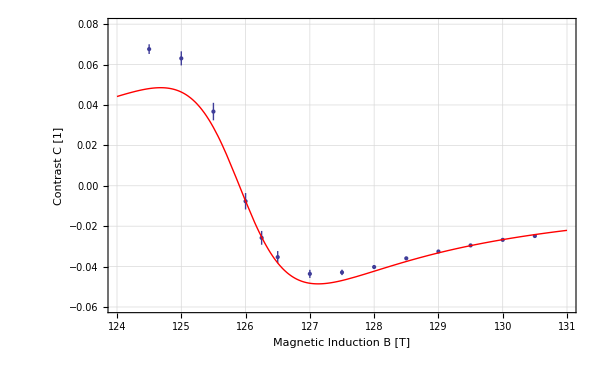

```mathematica
Show[ErrorListPlot[contrast],Plot[Normal[fita2all],{x,124,131},PlotStyle->Red],PlotRange->{-0.06,0.08},niceStyle,FrameLabel->{"Magnetic Induction B [T]","Contrast C [1]"}]
```

```mathematica
fita2=NonlinearModelFit[Drop[Drop[contrastᵀ,-1]ᵀ,3],(a*(x-c))/((x-c)^2+b),{a,b,{c,125}},x,
Weights->(Drop[contrast,3]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.99,
MaxIterations->1000000]
```

FittedModel[-(0.126703 (-125.796+x))/(2.1217+(-125.796+x)^2)]

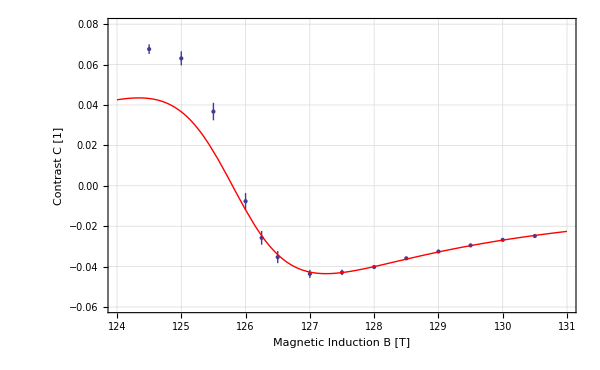

```mathematica
Show[ErrorListPlot[contrast],Plot[Normal[fita2],{x,124,131},PlotStyle->Red],PlotRange->{-0.06,0.08},niceStyle,FrameLabel->{"Magnetic Induction B [T]","Contrast C [1]"}]
```

```mathematica
fita2allred=NonlinearModelFit[Drop[Drop[contrastᵀ,-1]ᵀ,0],1/(a*(x-c)+b/(x-c)),{a,b,c},x,
Weights->(Drop[contrast,0]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.99,
MaxIterations->1000000]
```

FittedModel[1/(-12.6148/(-125.904+x)-8.40749 (-125.904+x))]

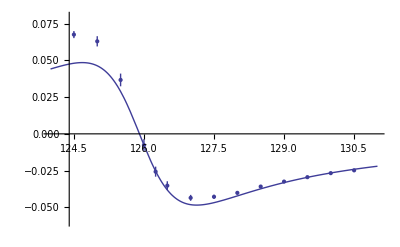

```mathematica
Show[ErrorListPlot[contrast],Plot[Normal[fita2allred],{x,124,131}],PlotRange->{-0.06,0.08}]
```

```mathematica
fita2red=NonlinearModelFit[Drop[Drop[contrastᵀ,-1]ᵀ,3],1/(a*(x-c)+b/(x-c)),{a,{b,-50},{c,125}},x,
Weights->(Drop[contrast,3]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
ConfidenceLevel->.95,
MaxIterations->1000000]
```

FittedModel[1/(-16.7454/(-125.796+x)-7.89246 (-125.796+x))]

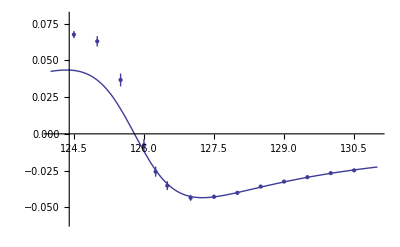

```mathematica
Show[ErrorListPlot[contrast],Plot[Normal[fita2red],{x,124,131}],PlotRange->{-0.06,0.08}]
```

### hopefully getting something out of the coefficients

this is the fit and the stuff calculated from the parameters from the fit to the straight part of the contrast

```mathematica
fita2invlin["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | -6.21136 | 0.239245 | -25.9623 | 0.0000130766
n | 770.343 | 30.9599 | 24.8819 | 0.0000154865

```mathematica
ErrorForm[{1/(4*m/.fita2invlin["BestFitParameters"]),(fita2invlin["ParameterErrors"]⟦1⟧)/(4*(m/.fita2invlin["BestFitParameters"])^2)},4]
```

-0.0402 ± 0.0016

```mathematica
ErrorForm[{(-(n/.fita2invlin["BestFitParameters"]))/(m/.fita2invlin["BestFitParameters"]),(n/.fita2invlin["BestFitParameters"])/(m/.fita2invlin["BestFitParameters"])*√(((fita2invlin["ParameterErrors"]⟦2⟧)/(n/.fita2invlin["BestFitParameters"]))^2+((fita2invlin["ParameterErrors"]⟦1⟧)/(m/.fita2invlin["BestFitParameters"]))^2)},4]
```

124.0220 ± 6.9040

this is the fit and the stuff calculated from the parameters from the fit to all points of the inverse contrast

```mathematica
fita2invall["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -7.79658 | 0.170162 | -45.8187 | 5.68763×10^-11
b | -16.983 | 0.899293 | -18.8849 | 6.39165×10^-8
c | 125.751 | 0.0690102 | 1822.21 | 9.2134×10^-24

```mathematica
ErrorForm[{1/(4*a/.fita2invall["BestFitParameters"]),(fita2invall["ParameterErrors"]⟦1⟧)/(4*(a/.fita2invall["BestFitParameters"])^2)},4]
```

-0.0321 ± 0.0007

```mathematica
ErrorForm[{(b/.fita2invall["BestFitParameters"])/(a/.fita2invall["BestFitParameters"])-1/(16*(a/.fita2invall["BestFitParameters"])^2),√((b/.fita2invall["BestFitParameters"])/(a/.fita2invall["BestFitParameters"])*√(((fita2invall["ParameterErrors"]⟦1⟧)/(a/.fita2invall["BestFitParameters"]))^2+((fita2invall["ParameterErrors"]⟦2⟧)/(b/.fita2invall["BestFitParameters"]))^2))^2+((√2*fita2invall["ParameterErrors"]⟦1⟧)/(16*(a/.fita2invall["BestFitParameters"])^3))^2},4]
```

2.1772 ± 0.1248

this is the fit and the stuff calculated from the parameters from the fit to the points of the inverse contrast without the three to the left of the singularity

```mathematica
fita2inv["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -8.4384 | 0.0808154 | -104.416 | 1.5908×10^-16
b | -9.22269 | 0.413945 | -22.28 | 7.45147×10^-10
c | 125.795 | 0.0305781 | 4113.89 | 1.77243×10^-32

```mathematica
ErrorForm[{1/(4*a/.fita2inv["BestFitParameters"]),(fita2invall["ParameterErrors"]⟦1⟧)/(4*(a/.fita2inv["BestFitParameters"])^2)},4]
```

-0.0296 ± 0.0006

```mathematica
ErrorForm[{(b/.fita2inv["BestFitParameters"])/(a/.fita2inv["BestFitParameters"])-1/(16*(a/.fita2inv["BestFitParameters"])^2),√((b/.fita2inv["BestFitParameters"])/(a/.fita2inv["BestFitParameters"])*√(((fita2inv["ParameterErrors"]⟦1⟧)/(a/.fita2inv["BestFitParameters"]))^2+((fita2inv["ParameterErrors"]⟦2⟧)/(b/.fita2inv["BestFitParameters"]))^2))^2+((√2*fita2inv["ParameterErrors"]⟦1⟧)/(16*(a/.fita2inv["BestFitParameters"])^3))^2},4]
```

1.0921 ± 0.0502

this is the fit and the stuff calculated from the parameters from the fit to all points of the contrast with the unreduced formula

```mathematica
fita2all["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.118942 | 0.0014542 | -81.7916 | 1.13666×10^-16
b | 1.50042 | 0.074426 | 20.1599 | 4.90662×10^-10
c | 125.904 | 0.0305856 | 4116.43 | 2.18432×10^-35

```mathematica
ErrorForm[{(a/.fita2all["BestFitParameters"])/4,(fita2all["ParameterErrors"]⟦1⟧)/4},4]
```

-0.0297 ± 0.0004

```mathematica
ErrorForm[{(b/.fita2all["BestFitParameters"])-((a/.fita2all["BestFitParameters"])/4)^2,√((fita2all["ParameterErrors"]⟦2⟧)^2+((√2*(a/.fita2all["BestFitParameters"])*fita2all["ParameterErrors"]⟦1⟧)/16)^2)},4]
```

1.4995 ± 0.0745

this is the fit and the stuff calculated from the parameters from the fit to all points of the contrast without the three leftmost datapoints with the unreduced formula

```mathematica
fita2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.126703 | 0.00230669 | -54.9285 | 1.33873×10^-11
b | 2.1217 | 0.140861 | 15.0624 | 3.73147×10^-7
c | 125.796 | 0.0504857 | 2491.72 | 7.53734×10^-25

```mathematica
ErrorForm[{(a/.fita2["BestFitParameters"])/4,(fita2["ParameterErrors"]⟦1⟧)/4},4]
```

-0.0317 ± 0.0006

```mathematica
ErrorForm[{(b/.fita2["BestFitParameters"])-((a/.fita2["BestFitParameters"])/4)^2,√((fita2["ParameterErrors"]⟦2⟧)^2+((√2*(a/.fita2["BestFitParameters"])*fita2["ParameterErrors"]⟦1⟧)/16)^2)},4]
```

2.1207 ± 0.1409

this is the fit and the stuff calculated from the parameters from the fit to all points of the contrast datapoints with the reduced formula

```mathematica
fita2allred["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -8.40749 | 0.102792 | -81.7916 | 1.13666×10^-16
b | -12.6148 | 0.51636 | -24.4302 | 6.18835×10^-11
c | 125.904 | 0.0305856 | 4116.43 | 2.18432×10^-35

```mathematica
ErrorForm[{1/(4*a/.fita2allred["BestFitParameters"]),(fita2allred["ParameterErrors"]⟦1⟧)/(4*(a/.fita2allred["BestFitParameters"])^2)},4]
```

-0.0297 ± 0.0004

```mathematica
ErrorForm[{(b/.fita2allred["BestFitParameters"])/(a/.fita2allred["BestFitParameters"])-1/(16*(a/.fita2allred["BestFitParameters"])^2),√((b/.fita2allred["BestFitParameters"])/(a/.fita2allred["BestFitParameters"])*√(((fita2allred["ParameterErrors"]⟦1⟧)/(a/.fita2allred["BestFitParameters"]))^2+((fita2allred["ParameterErrors"]⟦2⟧)/(b/.fita2allred["BestFitParameters"]))^2))^2+((√2*fita2allred["ParameterErrors"]⟦1⟧)/(16*(a/.fita2allred["BestFitParameters"])^3))^2},4]
```

1.4995 ± 0.0641

this is the fit and the stuff calculated from the parameters from the fit to all points of the contrast without the three leftmost datapoints with the reduced formula

```mathematica
fita2red["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -7.89246 | 0.143686 | -54.9285 | 1.33873×10^-11
b | -16.7454 | 0.85916 | -19.4905 | 4.98944×10^-8
c | 125.796 | 0.0504857 | 2491.72 | 7.53734×10^-25

```mathematica
ErrorForm[{1/(4*a/.fita2red["BestFitParameters"]),√((fita2red["ParameterErrors"]⟦1⟧)/(4*(a/.fita2red["BestFitParameters"])^2))},4]
```

-0.0317 ± 0.0241

```mathematica
ErrorForm[{(b/.fita2red["BestFitParameters"])/(a/.fita2red["BestFitParameters"])-1/(16*(a/.fita2red["BestFitParameters"])^2),√((b/.fita2red["BestFitParameters"])/(a/.fita2red["BestFitParameters"])*√(((fita2red["ParameterErrors"]⟦1⟧)/(a/.fita2red["BestFitParameters"]))^2+((fita2red["ParameterErrors"]⟦2⟧)/(b/.fita2red["BestFitParameters"]))^2))^2+((√2*fita2red["ParameterErrors"]⟦1⟧)/(16*(a/.fita2red["BestFitParameters"])^3))^2},4]
```

2.1207 ± 0.1156

## Angle Dependence

### making the contrast

```mathematica
(contrast3S=Replace[a3resultsS,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle/2//N,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm
```

45. | 0.0429384 | 0.00220099
42.5 | 0.0422705 | 0.00256441
40. | 0.0412926 | 0.00254486
37.5 | 0.039604 | 0.00263099
35. | 0.037859 | 0.00277474
32.5 | 0.0364546 | 0.00303809
30. | 0.0340237 | 0.00314298
27.5 | 0.0334302 | 0.00308799
25. | 0.029249 | 0.00335776
22.5 | 0.0280899 | 0.00298257
20. | 0.025641 | 0.00340259

```mathematica
(contrast3P=Replace[a3resultsP,{angle_,imax_,imin_,ierror_,offset_,offerror_}->{angle/2//N,(imax-imin)/(imax+imin+2*offset),(imax-imin)/(imax+imin+2*offset)√(((√(2*(ierror)^2))/(imax-imin))^2+((√(2*(ierror)^2+offerror^2))/(imax+imin+2*offset))^2)},2])//TableForm
```

20. | 0.02218 | 0.00134594
25. | 0.0273528 | 0.000985272
30. | 0.0315565 | 0.000906834
35. | 0.033957 | 0.000739504
40. | 0.0349809 | 0.000608191
45. | 0.0347705 | 0.000500134
42.5 | 0.0351348 | 0.00055151
37.5 | 0.0338213 | 0.00071986

### making the fits

```mathematica
fita3S=NonlinearModelFit[
Drop[Drop[contrast3Sᵀ,-1]ᵀ,0],{h+a Sin[ω((θ-δ )Degree)]},{h,a,ω,δ},θ,
Weights->(Drop[contrast3S,0]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&)
]
```

FittedModel[0.0260751+0.0178297 Sin[0.0511323 (-20.4683+θ)]]

```mathematica
fita3S["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 0.0260751 | 0.0753509 | 0.346049 | 0.739474
a | 0.0178297 | 0.0821443 | 0.217053 | 0.834357
ω | 2.92967 | 10.5698 | 0.277174 | 0.789653
δ | 20.4683 | 81.0406 | 0.252569 | 0.807857

```mathematica
morerrors=Replace[contrast3S,{angle_,contrastdingens_,error_}->{{angle,contrastdingens},ErrorBar[2,error]},2]
```

{{{45.,0.0429384},ErrorBar[2,0.00220099]},{{42.5,0.0422705},ErrorBar[2,0.00256441]},{{40.,0.0412926},ErrorBar[2,0.00254486]},{{37.5,0.039604},ErrorBar[2,0.00263099]},{{35.,0.037859},ErrorBar[2,0.00277474]},{{32.5,0.0364546},ErrorBar[2,0.00303809]},{{30.,0.0340237},ErrorBar[2,0.00314298]},{{27.5,0.0334302},ErrorBar[2,0.00308799]},{{25.,0.029249},ErrorBar[2,0.00335776]},{{22.5,0.0280899},ErrorBar[2,0.00298257]},{{20.,0.025641},ErrorBar[2,0.00340259]}}

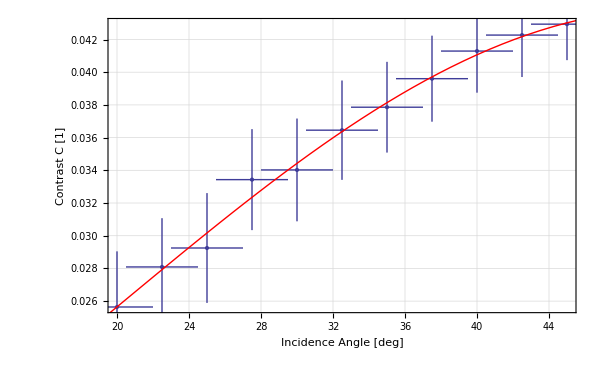

```mathematica
Show[ErrorListPlot[morerrors],Plot[Normal[fita3S],{θ,15,50},PlotStyle->Red],niceStyle2,FrameLabel->{"Incidence Angle [deg]","Contrast C [1]"}]
```

```mathematica
({Table[3,{i,11}]}~Join~{contrast3Sᵀ⟦3⟧})ᵀ
```

{{3,0.00220099},{3,0.00256441},{3,0.00254486},{3,0.00263099},{3,0.00277474},{3,0.00303809},{3,0.00314298},{3,0.00308799},{3,0.00335776},{3,0.00298257},{3,0.00340259}}

```mathematica
fita3P=NonlinearModelFit[
Drop[Drop[contrast3Pᵀ,-1]ᵀ,0],{a Cos[ω((θ-δ) Degree)]},{a,{ω,1.4},δ},θ,
Weights->(Drop[contrast3P,0]ᵀ⟦3⟧)^-2,
VarianceEstimatorFunction->(1&),
MaxIterations->1000000
]
```

FittedModel[0.0350345 Cos[0.0399714 (-41.8896+θ)]]

```mathematica
fita3P["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0350345 | 0.000278997 | 125.573 | 6.07474×10^-10
ω | 2.29019 | 0.216521 | 10.5772 | 0.000130534
δ | 41.8896 | 1.49789 | 27.9658 | 1.09455×10^-6

```mathematica
morerrorp=Replace[contrast3P,{angle_,contrastdingens_,error_}->{{angle,contrastdingens},ErrorBar[2,error]},2]
```

{{{20.,0.02218},ErrorBar[2,0.00134594]},{{25.,0.0273528},ErrorBar[2,0.000985272]},{{30.,0.0315565},ErrorBar[2,0.000906834]},{{35.,0.033957},ErrorBar[2,0.000739504]},{{40.,0.0349809},ErrorBar[2,0.000608191]},{{45.,0.0347705},ErrorBar[2,0.000500134]},{{42.5,0.0351348},ErrorBar[2,0.00055151]},{{37.5,0.0338213},ErrorBar[2,0.00071986]}}

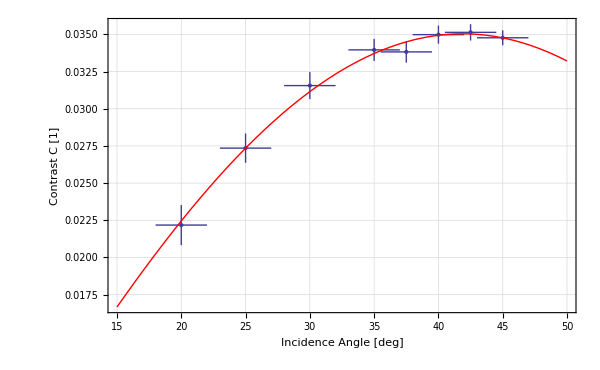

```mathematica
Show[ErrorListPlot[morerrorp],Plot[Normal[fita3P],{θ,15,50},PlotStyle->Red],PlotRange->All,niceStyle2,FrameLabel->{"Incidence Angle [deg]","Contrast C [1]"}]
```

## Kerr Microscopy

```mathematica
imgnodom=Import["./raw_data/bilder1/2.bmp"];
```

```mathematica
imgmanydom=Import["./raw_data/bilder1/0.bmp"];
```

```mathematica
imgmanydomneg=Import["./raw_data/bilder1/0neg.bmp"];
```

```mathematica
imgnodomneg=Import["./raw_data/bilder1/1neg.bmp"];
```

GaussianFilter[ImageAdjust[ImageSubtract[imgnodom, imgmanydom], {2.0, 4.5}], 3] war ein erster Versuch, aber ImageAdjust arbeitet deutlich besser wenn man ihm nicht sagt, was es tun soll

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[imgnodom,imgmanydom]],3]],{480,Full},Right]
```

```mathematica
ErrorForm[{40*8/135//N,(40*8)/135 √((2/8)^2+(5/135)^2)//N},1]
```

2.4 ± 0.6

```mathematica
ErrorForm[{80*8/135//N,(80*8)/135 √((2/8)^2+(5/135)^2)//N},1]
```

4.7 ± 1.2

```mathematica
ImagePartition[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[imgnodom,imgmanydom]],3]],32]//Grid
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[imgmanydomneg,imgnodomneg]],3]],{480,Full},Right]
```

```mathematica
haar1=Import["./raw_data/bilder2/b/haar1.bmp"];
```

```mathematica
haar2=Import["./raw_data/bilder2/b/haar2.bmp"];
```

```mathematica
haar3=Import["./raw_data/bilder2/b/haar3.bmp"];
```

```mathematica
haar5=Import["./raw_data/bilder2/b/haar5.bmp"];
```

```mathematica
haar6=Import["./raw_data/bilder2/b/haar6.bmp"];
```

```mathematica
haar7=Import["./raw_data/bilder2/b/haar7.bmp"];
```

```mathematica
haar8=Import["./raw_data/bilder2/b/haar8.bmp"];
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar2]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar3]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar5]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar6]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar7]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar1,haar8]],2]],{480,Full},Right]
```

```mathematica
haar1a=Import["./raw_data/bilder2/a/haar1a.bmp"];
```

```mathematica
haar2a=Import["./raw_data/bilder2/a/haar2a.bmp"];
```

```mathematica
haar3a=Import["./raw_data/bilder2/a/haar3a.bmp"];
```

```mathematica
haar4a=Import["./raw_data/bilder2/a/haar4a.bmp"];
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar2a,haar1a]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar3a,haar1a]],2]],{480,Full},Right]
```

```mathematica
ImageCrop[ImageAdjust[GaussianFilter[ImageAdjust[ImageSubtract[haar4a,haar1a]],2]],{480,Full},Right]
```